## Задача 1

Уравнение Шреденгера для атома водорода имеет вид:
-h^2/(2 mr^2)(r^2 ψ')'-e^2/r ψ=E ψ[x]
-r^2ψ''-2rψ'-rψ=r^2 E ψ[x]

```mathematica
m = 1;
ℏ = 1;
e = 1;
l=0;
-1/(2 m)ψ''[r] -2/r ψ'[r]+(2m)/ℏ^2(-e^2/r-EE)ψ[r]+(l(l+1))/(2m r^2)ψ[r]
```

2 (-0.1-1/r) ψ[r]-(2 ψ'[r])/r-ψ''[r]/2

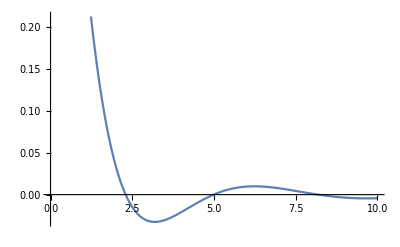

```mathematica
EE=0.1;
solution=NDSolve[{-1/(2 m)ψ''[r] -2/r ψ'[r]+(2m)/ℏ^2(-e^2/r-EE)ψ[r]+(l(l+1))/(2m r^2)ψ[r]==0,ψ[10^(-8)]==1,ψ'[10^(-8)]==0},
ψ,{r,10^(-8),10}][[1]];
Plot[ψ[r]/.solution,{r,10^(-8),10}]
```

```mathematica
Manipulate[
solution=NDSolve[{-1/(2 m)ψ''[r] -2/r ψ'[r]+(2m)/ℏ^2(-e^2/r-EE)ψ[r]+(l(l+1))/(2m r^2)ψ[r]==0,ψ[10^(-8)]==1,ψ'[10^(-8)]==0},
ψ,{r,10^(-8),10}][[1]];
Plot[ψ[r]/.solution,{r,10^(-8),10}],
{EE,-1,1}
]
```

```mathematica
solution=NDSolve[{-1/(2 m)ψ''[r] -2/r ψ'[r]+(2m)/ℏ^2(-e^2/r-EE)ψ[r]+(l(l+1))/(2m r^2)ψ[r]==0,ψ[10^(-8)]==1,ψ'[10^(-8)]==0},
ψ,{r,10^(-8),10}][[1]];
Plot[ψ[r]/.solution,{r,10^(-8),10}]
```

## Задача 2

```mathematica
x/:x^m_:=-x^(m-2)/; (m≥2)
```

```mathematica
p[x_]:=x^5-6 x^4+5 x^3+10 x^2-x+1
```

```mathematica
p[x]
```

```mathematica
-15-5 x
```

## Задача 3

```mathematica
i /:
i^2:= -1
j /:
j^2:= -1
k /:
k^2:= -1
i j ^:= k
j k ^:= i
k i ^:= j
```

```mathematica
L1 = 5 + 6i + 7j + 10 k;
L2 = 15 + 3i + 31j + 4 k;
L1 + L2
```

20+9 i+38 j+14 k

```mathematica
Expand[L1*L2]
```

-200+443 i+314 j+377 k

## Задача 4

```mathematica
HamEq[H_,coord_]:= Module[{n,i,equations},
n=Length[coord];
equations=Table[0,{i1,n},{j1,2}];
For[i=1,i≤n,i++,
equations[[i,1]]=- D[H,coord[[i,1]][t] ];
equations[[i,2]]= D[H,coord[[i,2]][t] ]
];
equations
];
```

```mathematica
H0=p1[t]^2/(2m1)+p2[t]^2/(2m2)+(c0/2)[q1[t]^2 + q2[t]^2 ] ;
HamEq[H0,{{q1,p1},{q2,p2}}]
```

{{-2 q1[t] (c0/2)'[q1[t]^2+q2[t]^2],p1[t]/m1},{-2 q2[t] (c0/2)'[q1[t]^2+q2[t]^2],p2[t]/m2}}

## Задача 5

```mathematica
HamJacEq[H_,coord_]:=
Module[{n,i,equation,newc,rule0,rule1,rule2,SS},
n=Length[coord];
newc=StringRiffle[Table[coord[[i,1]],{i,1,n}],","];
SS=ToExpression["S["<>newc<>",t]"];
rule1=Table[coord[[i,2]][t]->D[SS,coord[[i,1]]],{i,1,n}];
rule0=Table[coord[[i,1]][t]->coord[[i,1]],{i,1,n}];
rule2=Table[coord[[i,1]]->coord[[i,1]][t],{i,1,n}];
equation=H/.rule0/.rule1;
equation=equation+D[SS,t];
Return[equation/.rule2]
];
```

```mathematica
HamJacEq[H0,{{q1,p1},{q2,p2}}]
```

c0/2[q1[t]^2+q2[t]^2]+S^(0,0,1)[q1[t],q2[t],t]+((S^(0,1,0)[q1[t],q2[t],t])^2)/(2 m2)+((S^(1,0,0)[q1[t],q2[t],t])^2)/(2 m1)